# Modelización Matemática - Tema 4

## Diego Ángel Gallardo Costilla

## Ejercicio 4.1

Diferenciamos tres casos “interesantes”: si , diverge, si  converge a 0 oscilando y si  oscila entre -1 y 1. Se observan los tres casos en la gráfica.

```mathematica
x0 = 3;
f[x_]:=1.3x;
l1 = NestList[f,x0,15]
```

{3,3.9,5.07,6.591,8.5683,11.1388,14.4804,18.8246,24.4719,31.8135,41.3575,53.7648,69.8943,90.8625,118.121,153.558}

```mathematica
x0 = 5;
f[x_]:=-0.8x;
l2 = NestList[f,x0,15]
```

{5,-4.,3.2,-2.56,2.048,-1.6384,1.31072,-1.04858,0.838861,-0.671089,0.536871,-0.429497,0.343597,-0.274878,0.219902,-0.175922}

```mathematica
x0 = 5;
f[x_]:=-1x;
l3 = NestList[f,x0,15]
```

{5,-5,5,-5,5,-5,5,-5,5,-5,5,-5,5,-5,5,-5}

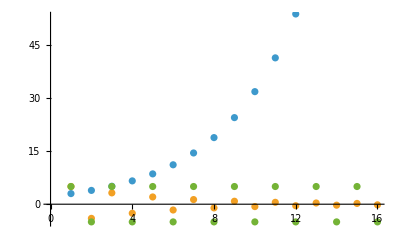

```mathematica
ListPlot[{l1,l2,l3}]
```

## Ejercicio 4.3

```mathematica
Otro ejercicio
```

## Ejercicio 4.6

```mathematica
x0 = 0.51;
f[x_]:=r x(1-x);
```

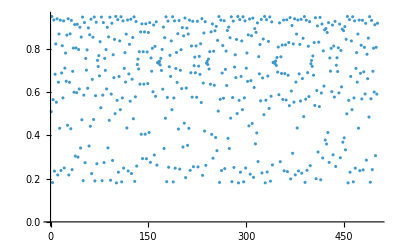

```mathematica
l3 = NestList[f,x0,500];
ListPlot[l3]
```

```mathematica
f2[x_]:=f[f[x]]
sol = Solve[f2[x]==x,x]
```

{{x→0},{x→(-1+r)/r},{x→(r+r^2-r √(-3-2 r+r^2))/(2 r^2)},{x→(r+r^2+r √(-3-2 r+r^2))/(2 r^2)}}

Vemos que  y viceversa.

```mathematica
F[sol[[3]]]
```

F[{x→0.736842}]

```mathematica
datos=ParallelTable[f=# (r (1-#))&;
listapuntos=NestList[f,0.5,500];
Thread[{r,Drop[listapuntos,100]}],{r,3,4,0.001}];

ListPlot[Flatten[datos,1],PlotStyle->{PointSize[0.001],Blue},AxesLabel->{"r","x_n"},PlotLabel->"Diagrama de Bifurcación (x0 = 0.5)"]
```

-Graphics-